# Fast Gates on a Transmon

A transmon is a superconducting circuit that behaves as a weakly anharmonic oscillator. A qubit is stored in its two lowest levels, and a microwave pulse at the qubit frequency rotates it between them. The anharmonicity is small, a few hundred megahertz against a qubit frequency of several gigahertz, so the transition from |1⟩ to |2⟩ lies close to the qubit transition. A short pulse has a broad spectrum and drives both, carrying population out of the qubit. A long pulse avoids that but is exposed for longer to energy decay and dephasing.

How long the best pulse is, and how much the derivative correction known as DRAG shortens it, has no closed-form answer. Both follow from the Schrödinger and Lindblad equations solved with the levels the qubit leaks into kept explicitly. For an anharmonicity of −200 MHz and coherence times T_1 and T_2 of 100 μs, the best π pulse below lasts 17.7 ns with an error of 9.8 × 10⁻⁵ when it uses DRAG, against 2.0 × 10⁻⁴ near 32 ns without it.

## Five Levels of a Transmon

In the frame rotating at the qubit frequency, the transmon is the anharmonic oscillator H_0=α/2 b^†b^†bb, where b lowers the excitation number by one and α is the anharmonicity. Five levels are kept here; the last section shows that fewer change the answer and more do not.

The lowering operator of a five-level oscillator:

```mathematica
b = AnnihilationOperator[5]
```

QuantumOperator[…]

In the rotating frame the qubit levels |0⟩ and |1⟩ are degenerate, and the higher levels are shifted by α, 3α and 6α:

```mathematica
MatrixForm[Normal[((α/2) (SuperDagger[b] @ SuperDagger[b] @ b @ b))["Matrix"]]]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | α | 0 | 0
0 | 0 | 0 | 3 α | 0
0 | 0 | 0 | 0 | 6 α)

A drive couples neighboring levels with strengths 1, √2, √3 and 2, so it drives the transition from |1⟩ to |2⟩ more strongly than the qubit transition:

```mathematica
MatrixForm[Normal[(b + SuperDagger[b])["Matrix"]]]
```

(0 | 1 | 0 | 0 | 0
1 | 0 | √2 | 0 | 0
0 | √2 | 0 | √3 | 0
0 | 0 | √3 | 0 | 2
0 | 0 | 0 | 2 | 0)

## The Pulse

The drive has the cosine envelope Ω(t)=π/τ(1-cos (2πt)/τ), which starts and ends at zero. DRAG (Motzoi, Gambetta, Rebentrost and Wilhelm, 2009) adds an out-of-phase quadrature proportional to the derivative of the envelope, and a detuning δ moves the drive off the qubit frequency:

H(t)=α/2 b^†b^†bb+δ b^†b+(Ω(t))/2(b+b^†)-(λ Ω̇(t))/(2α)i(b^†-b)

The envelope, with τ the pulse length:

```mathematica
envelope = (Pi/τ) (1 - Cos[2 Pi t/τ])
```

(π (1-Cos[(2 π t)/τ]))/τ

Its area is π for every length, which makes it a π pulse:

```mathematica
Integrate[envelope, {t, 0, τ}]
```

π

The whole Hamiltonian as one operator, with the anharmonicity, the DRAG coefficient, the detuning and the pulse length kept as parameters:

```mathematica
model = QuantumOperator[
  (α/2) (SuperDagger[b] @ SuperDagger[b] @ b @ b) + δ (SuperDagger[b] @ b) +
    (envelope/2) (b + SuperDagger[b]) - (λ D[envelope, t]/(2 α)) (I (SuperDagger[b] - b)),
  "Parameters" -> {α, λ, δ, τ}]
```

QuantumOperator[…]

Numbers enter by supplying the parameters in that order. Times are in nanoseconds and frequencies in radians per nanosecond, so an anharmonicity of −200 MHz is:

```mathematica
anharmonicity = -2 Pi 0.2
```

-1.25664

## Leakage

An 8 ns pulse without DRAG or detuning, starting from |0⟩:

```mathematica
psi = QuantumEvolve[model[anharmonicity, 0, 0, 8], FockState[0, 5], {t, 0, 8}]
```

QuantumState[…]

The populations of the three lowest levels during the pulse:

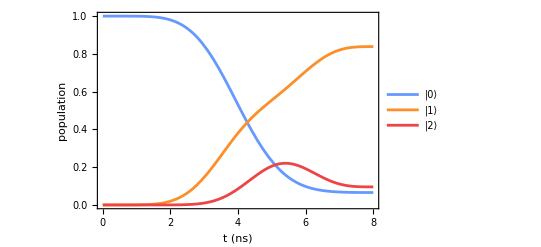

```mathematica
Plot[Evaluate[psi[t]["ProbabilitiesList"][[;; 3]]], {t, 0, 8},
  PlotStyle -> {StandardBlue, StandardOrange, StandardRed},
  PlotLegends -> {"|0⟩", "|1⟩", "|2⟩"},
  Frame -> True, FrameLabel -> {"t (ns)", "population"}]
```

Population passes through |2⟩ on its way to |1⟩, and part of it stays there. At the end of the pulse 9.6% of the population is in |2⟩:

```mathematica
psi[8]["ProbabilitiesList"]
```

{0.0657671,0.838515,0.0956994,0.0000183186,1.90366×10^-10}

Pulses are compared through a function of the three controls. Numeric code here names them drag, detuning and length rather than λ, δ and τ: Tablepaclet:ref/Table and FindMinimumpaclet:ref/FindMinimum localize their variables dynamically, so iterating over τ would also set it inside model. The final populations for a given DRAG coefficient, detuning and length:

```mathematica
populations[drag_?NumericQ, detuning_?NumericQ, length_?NumericQ] :=
  QuantumEvolve[model[anharmonicity, drag, detuning, length], FockState[0, 5], {t, 0, length}][length]["ProbabilitiesList"]
```

Leakage into |2⟩ for pulses from 4 to 24 ns:

```mathematica
leakageTable = Table[{length, populations[0, 0, length][[3]]}, {length, {4, 6, 8, 12, 16, 24}}]
```

{{4,0.583254},{6,0.30998},{8,0.0956994},{12,0.00064026},{16,0.000179682},{24,0.0000105546}}

On a logarithmic scale:

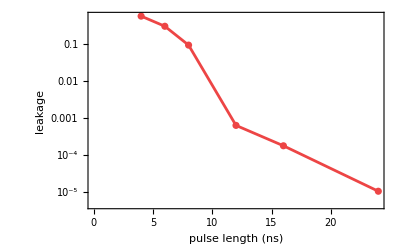

```mathematica
ListLogPlot[leakageTable, Joined -> True, Mesh -> All, PlotStyle -> StandardRed,
  Frame -> True, FrameLabel -> {"pulse length (ns)", "leakage"}]
```

Leakage falls by more than four orders of magnitude between 4 and 24 ns, but even at 24 ns a pulse without DRAG leaves 1.1 × 10⁻⁵ of the population in |2⟩.

## DRAG

To first order in 1/α, the DRAG quadrature removes the leakage at λ = 1. The transfer error counts the population that does not reach |1⟩, leakage included. Leakage and transfer error at 8 ns for λ = 0, 1/2 and 1:

```mathematica
Table[With[{p = populations[drag, 0, 8]}, {drag, p[[3]], 1 - p[[2]]}], {drag, {0, 1/2, 1}}]
```

{{0,0.0956994,0.161485},{1/2,0.0262962,0.0293745},{1,0.00116017,0.0810995}}

λ = 1 cuts the leakage by a factor of 80 but leaves 8% of the population short of |1⟩. A scan over λ shows the two errors reaching their minima at different values:

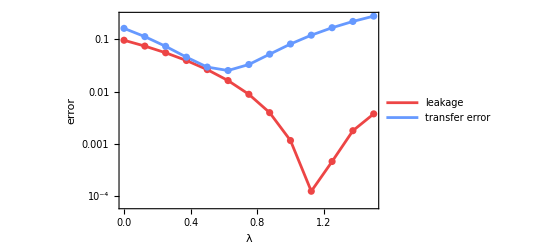

```mathematica
ListLogPlot[
  Transpose @ Table[With[{p = populations[drag, 0, 8]}, {{drag, p[[3]]}, {drag, 1 - p[[2]]}}], {drag, 0, 1.5, 0.125}],
  Joined -> True, Mesh -> All, PlotStyle -> {StandardRed, StandardBlue},
  PlotLegends -> {"leakage", "transfer error"}, Frame -> True, FrameLabel -> {"λ", "error"}]
```

The leakage is smallest just above λ = 1, and the transfer error near λ = 0.6, so no single λ serves both. A detuning δ added to the search resolves this. The transfer error as a function of the three controls:

```mathematica
transferError[drag_?NumericQ, detuning_?NumericQ, length_?NumericQ] := 1 - populations[drag, detuning, length][[2]]
```

The best DRAG coefficient and detuning for a 12 ns pulse:

```mathematica
optimum = FindMinimum[transferError[drag, detuning, 12], {{drag, 0.75}, {detuning, 0.03}}, Method -> "PrincipalAxis"]
```

{0.000213634,{drag→0.695828,detuning→0.0297045}}

The transfer error falls to 2.1 × 10⁻⁴ at λ = 0.70 and a detuning of 0.030 rad/ns, 4.7 MHz. Without DRAG, the best detuning at 12 ns leaves ten times the error:

```mathematica
noDRAG = FindMinimum[transferError[0, detuning, 12], {detuning, 0}, Method -> "PrincipalAxis"]
```

{0.00205459,{detuning→-0.0731277}}

## Decoherence and the Best Pulse Length

Leakage falls with the pulse length, and decay and dephasing grow with it. Energy decay enters as the jump operator b at rate 1/T_1, which empties level n at rate n/T_1. Pure dephasing enters as b^†b at rate 2/T_ϕ, with 1/T_ϕ=1/T_2-1/(2 T_1). Both coherence times, 100 μs, in nanoseconds:

```mathematica
T1 = T2 = 100000
```

100000

The pure dephasing time:

```mathematica
dephasingTime = 1/(1/T2 - 1/(2 T1))
```

200000

The transfer error with decay and dephasing, from the Lindblad master equation:

```mathematica
openError[drag_?NumericQ, detuning_?NumericQ, length_?NumericQ] :=
  1 - QuantumEvolve[model[anharmonicity, drag, detuning, length],
      {b, SuperDagger[b] @ b} -> {1/T1, 2/dephasingTime}, FockState[0, 5], {t, 0, length}][length]["ProbabilitiesList"][[2]]
```

At the 12 ns optimum, decoherence adds 6 × 10⁻⁵:

```mathematica
openError[drag /. Last[optimum], detuning /. Last[optimum], 12]
```

0.000276822

Across pulse lengths, λ is held at its 12 ns optimum: it is dimensionless, and the derivative term scales with the pulse by itself. The detuning compensates a shift that grows with the drive power, which goes as 1/τ^2, so it is optimized again at each length, starting from the 12 ns value scaled by (12/τ)^2. The error with decoherence at the best detuning:

```mathematica
bestError[drag_?NumericQ, reference_?NumericQ, length_?NumericQ] :=
  With[{opt = FindMinimum[transferError[drag, detuning, length], {detuning, reference (12/length)^2}, Method -> "PrincipalAxis"]},
    openError[drag, detuning /. Last[opt], length]]
```

With DRAG:

```mathematica
withDRAG = Table[{length, bestError[drag /. Last[optimum], detuning /. Last[optimum], length]}, {length, {10, 12, 16, 24, 40}}]
```

{{10,0.0039519},{12,0.000276822},{16,0.000107017},{24,0.000122584},{40,0.000200702}}

Without DRAG:

```mathematica
withoutDRAG = Table[{length, bestError[0, detuning /. Last[noDRAG], length]}, {length, {12, 16, 24, 40, 60}}]
```

{{12,0.0021182},{16,0.000805392},{24,0.000249762},{40,0.000217021},{60,0.000303393}}

The error against pulse length, with and without DRAG:

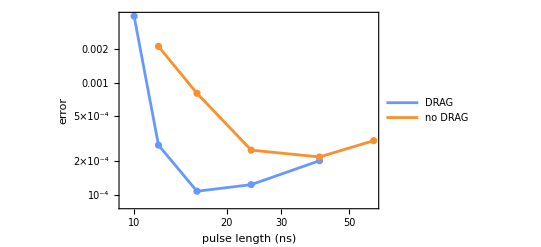

```mathematica
ListLogLogPlot[{withDRAG, withoutDRAG}, Joined -> True, Mesh -> All,
  PlotStyle -> {StandardBlue, StandardOrange}, PlotLegends -> {"DRAG", "no DRAG"},
  Frame -> True, FrameLabel -> {"pulse length (ns)", "error"}]
```

Both curves have a minimum: to its left leakage and the residual shift dominate, to its right decay and dephasing. FindMinimumpaclet:ref/FindMinimum locates it. With DRAG:

```mathematica
FindMinimum[bestError[drag /. Last[optimum], detuning /. Last[optimum], length], {length, 16, 20}]
```

{0.0000984328,{length→17.7381}}

Without DRAG:

```mathematica
FindMinimum[bestError[0, detuning /. Last[noDRAG], length], {length, 30, 40}]
```

{0.000200115,{length→31.7138}}

DRAG roughly halves both the pulse length and its error, from 32 ns to 17.7 ns and from 2.0 × 10⁻⁴ to 9.8 × 10⁻⁵. The minimum without DRAG is flat. Started from 35 ns instead, the search stops at another length with almost the same error:

```mathematica
FindMinimum[bestError[0, detuning /. Last[noDRAG], length], {length, 35, 45}]
```

{0.000202814,{length→34.8898}}

Its location is soft and its value is not.

## Five Levels Are Enough

Every result above keeps five levels. The leakage of the 8 ns pulse without DRAG, for a transmon truncated to d levels:

```mathematica
leakageWithLevels[d_] := With[{a = AnnihilationOperator[d]},
  QuantumEvolve[(anharmonicity/2) (SuperDagger[a] @ SuperDagger[a] @ a @ a) + ((envelope /. τ -> 8)/2) (a + SuperDagger[a]),
    FockState[0, d], {t, 0, 8}][8]["ProbabilitiesList"][[3]]]
```

From three to six levels:

```mathematica
Table[{d, leakageWithLevels[d]}, {d, 3, 6}]
```

{{3,0.0513115},{4,0.0941426},{5,0.0956994},{6,0.0957147}}

Three levels underestimate the leakage by almost half. Five and six agree to within 0.02%.

Related Guides

WolframQuantumComputationFrameworkpaclet:Wolfram/QuantumFramework/guide/WolframQuantumComputationFramework

Related Tech Notes

TimeEvolutionpaclet:Wolfram/QuantumFramework/tutorial/TimeEvolution ▪ SecondQuantizationpaclet:Wolfram/QuantumFramework/tutorial/SecondQuantization

## Metadata

### Categorization

Tutorial

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/TransmonGates

### Keywords

transmon

superconducting qubit

leakage

DRAG

pi pulse

anharmonicity

gate error

pulse length

Lindblad

decoherence

T1

T2

qudit

optimization